# Heat stress and bleaching in corals: a bioenergetic model

## Pfab et al, 2024 ferdinand.pfab@gmail.com Code for steady state plots

```mathematica
Get[NotebookDirectory[]<>#]&/@{
(*load model definition*)
"23_10_04_simulation_1.m",
(*load parameter values*)
"23_10_04_parameters_1.m",
(*load functions and options for simulations and plots*)
"23_10_04_styles_1.m"
};
```

```mathematica
Tmin=20;Tmax=40;
rangeTFinalStatePlot=Range[Tmin,Tmax,1/20(Tmax-Tmin)];
yranges=({jHGm->{0,jHGmmax},jSGm->{0,jSGmmax}, jCPm->{0,jCPmmax},_->Full}/.SUmaxs);

finalplotoptionss={_->{Ticks->{Range[Tmin+1,Tmax,2],ticksmanual},AxesOrigin->{Automatic,0}}};
```

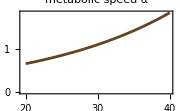
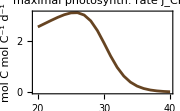
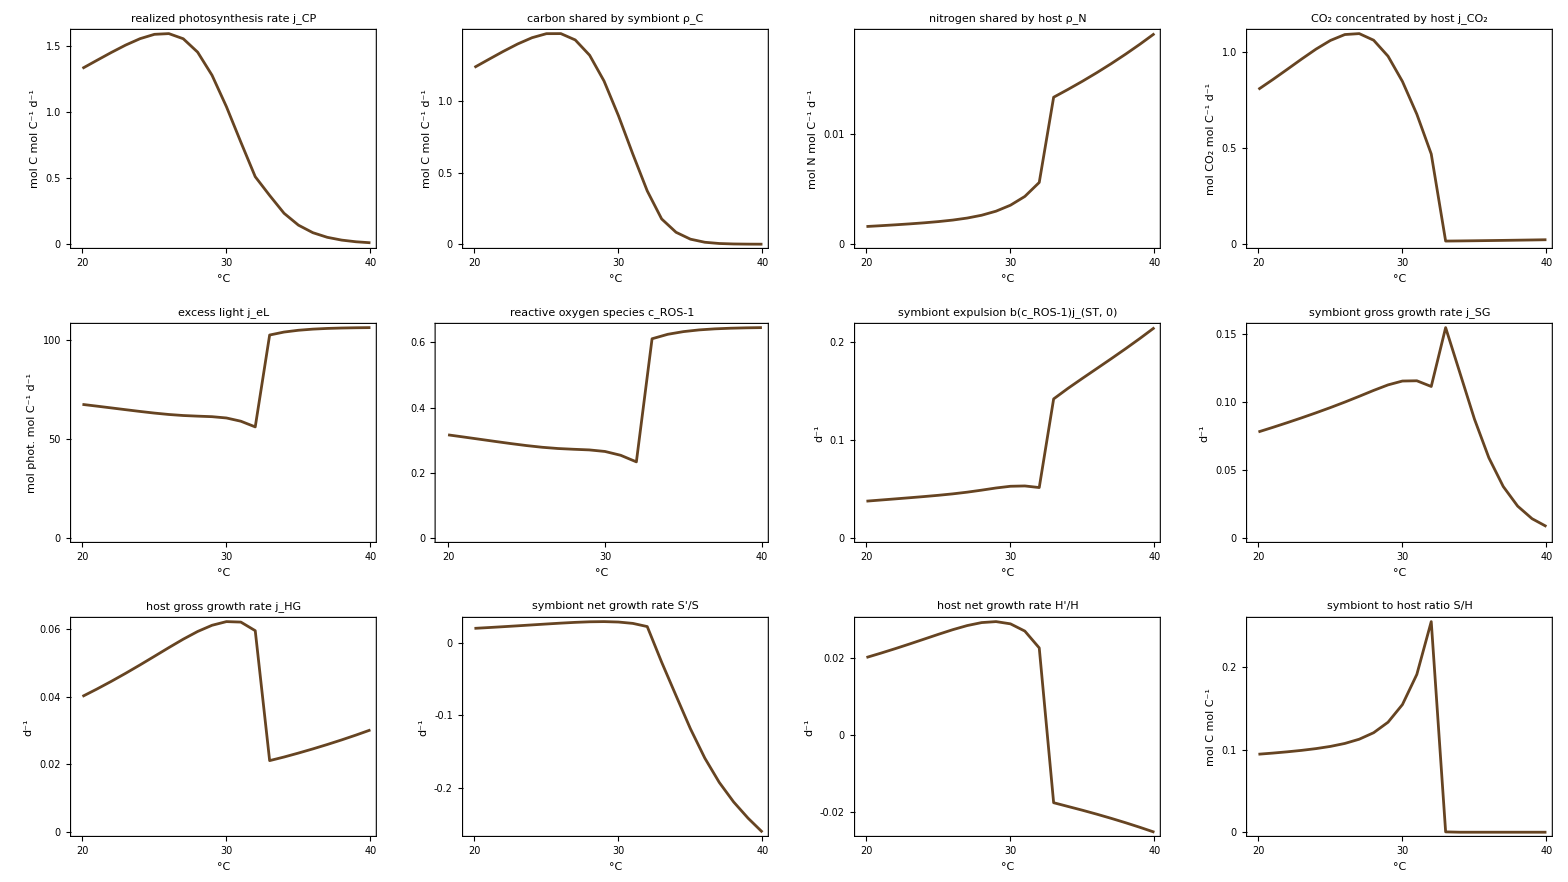
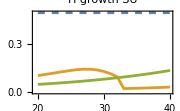
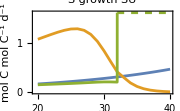
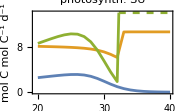
-Graphics--Graphics-
-Graphics-
-Graphics-
-Graphics--Graphics--Graphics-

```mathematica
(*Fig. 5, S11*)
finalplot["steadystate-FvFm-Arr.pdf",parvalsFvFmArr,T,rangeTFinalStatePlot,inivalsdefault,yranges,arrangementFinalStatePlot,finalplotoptionss,1]
```

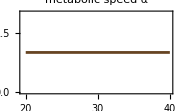
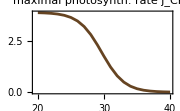
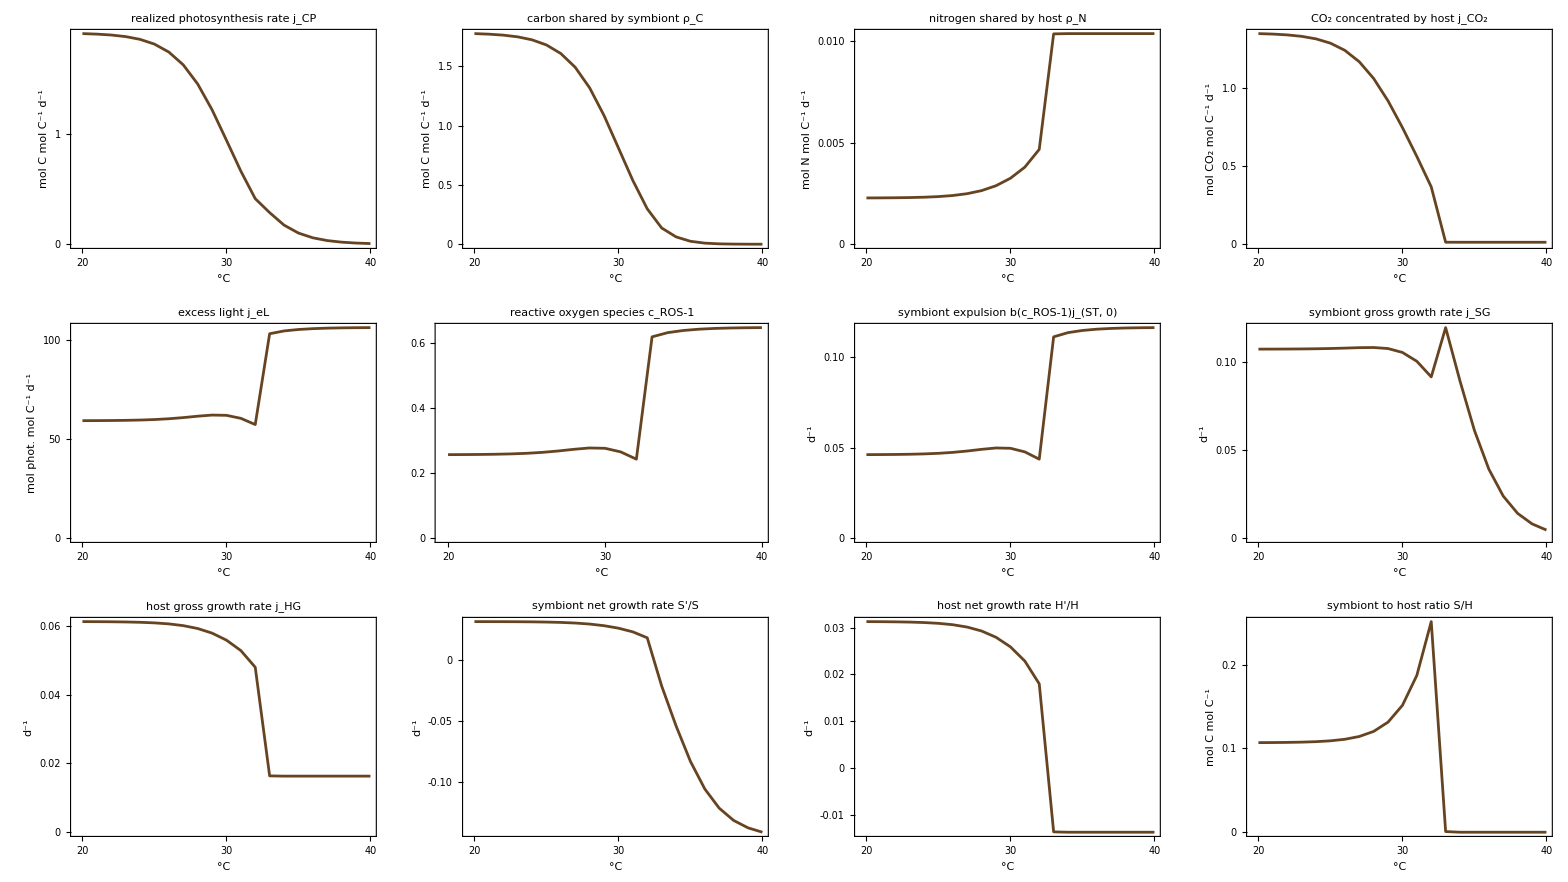
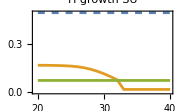
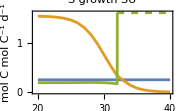
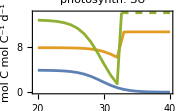
-Graphics--Graphics-
-Graphics-
-Graphics-
-Graphics--Graphics--Graphics-

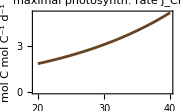
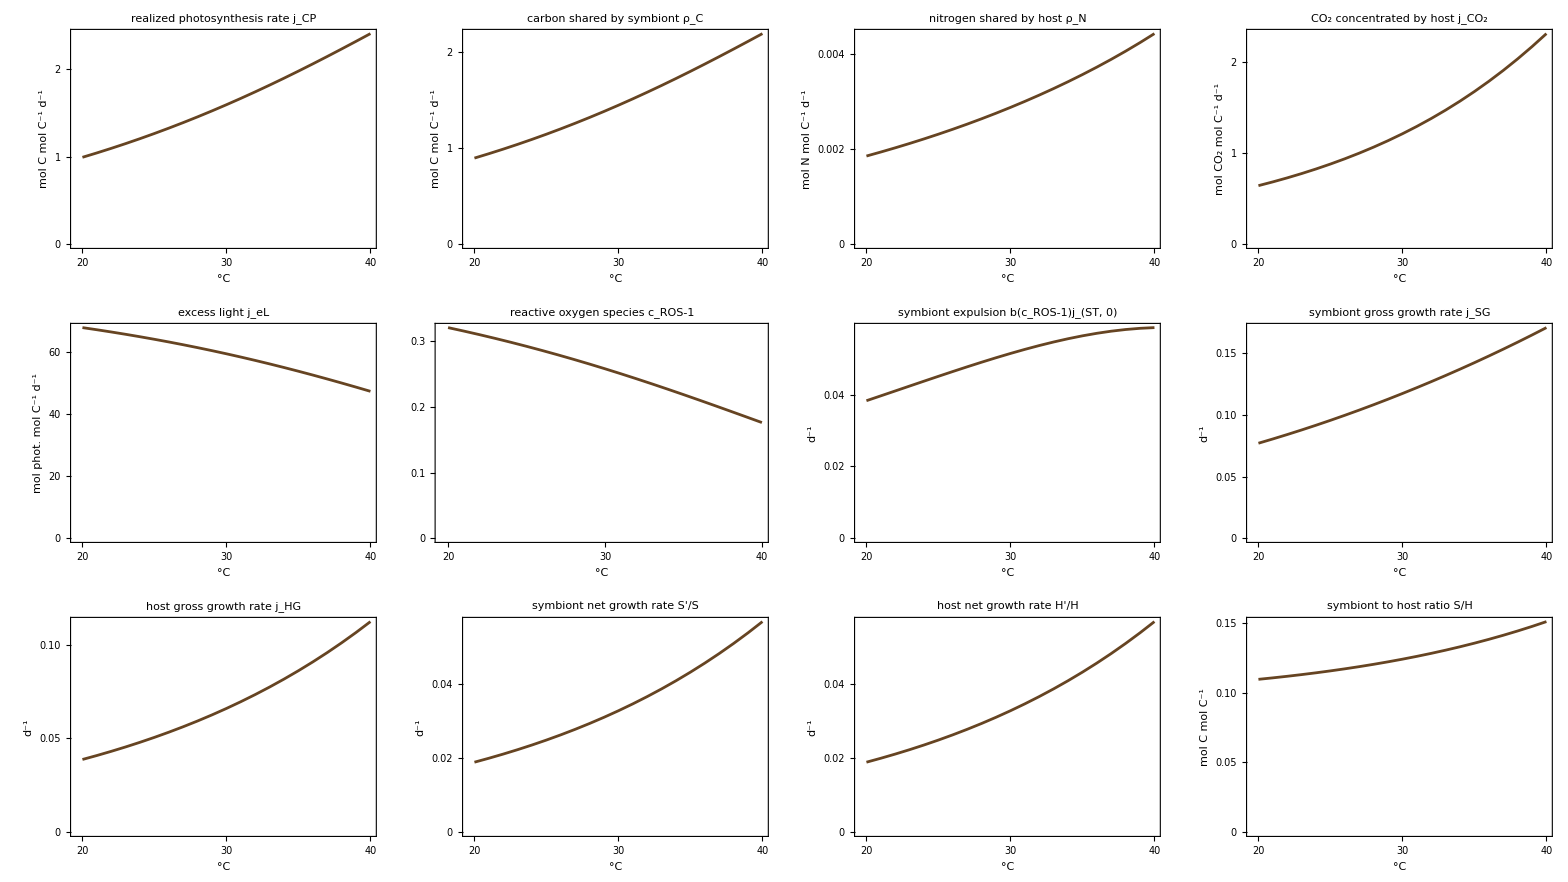
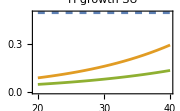
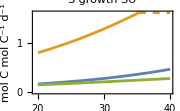
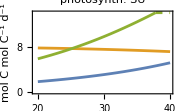
-Graphics--Graphics-
-Graphics-
-Graphics-
-Graphics--Graphics--Graphics-

```mathematica
(*Fig. S11*)
finalplot["steadystate-FvFm.pdf",parvalsFvFm,T,rangeTFinalStatePlot,inivalsdefault,yranges,arrangementFinalStatePlot,finalplotoptionss,1]
finalplot["steadystate-Arr.pdf",parvalsArr,T,rangeTFinalStatePlot,inivalsdefault,Join[{jCP->{0,1.2}},yranges],arrangementFinalStatePlot,finalplotoptionss,1]
```

```mathematica
(*Fig. S12*)
arrangementFinalStatePlotN=Framed[Column[{Multicolumn[#1⟦3;;-4⟧,4,Appearance->"Horizontal"],Row[#1⟦-3;;-1⟧]},Alignment->Center],RoundingRadius->framingRadius]&;
```

```mathematica
NRangemin= .1 10^-6.;NRangemax=  6 10^-6.;
rangeΝFinalStatePlot=Range[NRangemin,NRangemax,1/20(NRangemax-NRangemin)];
```

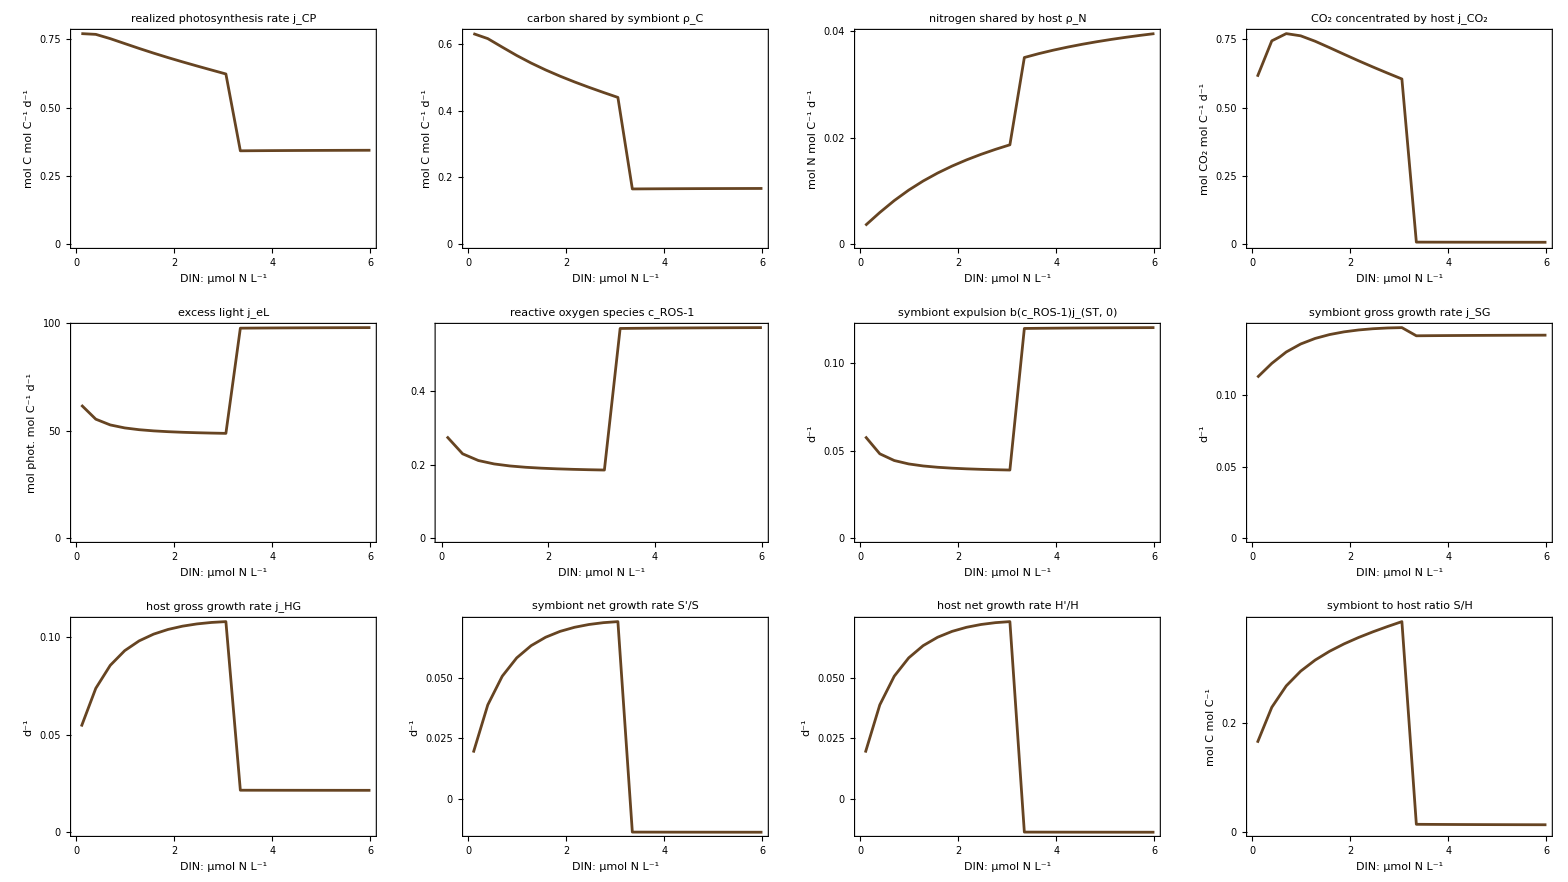
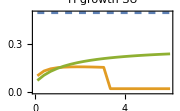
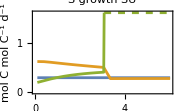
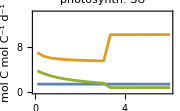

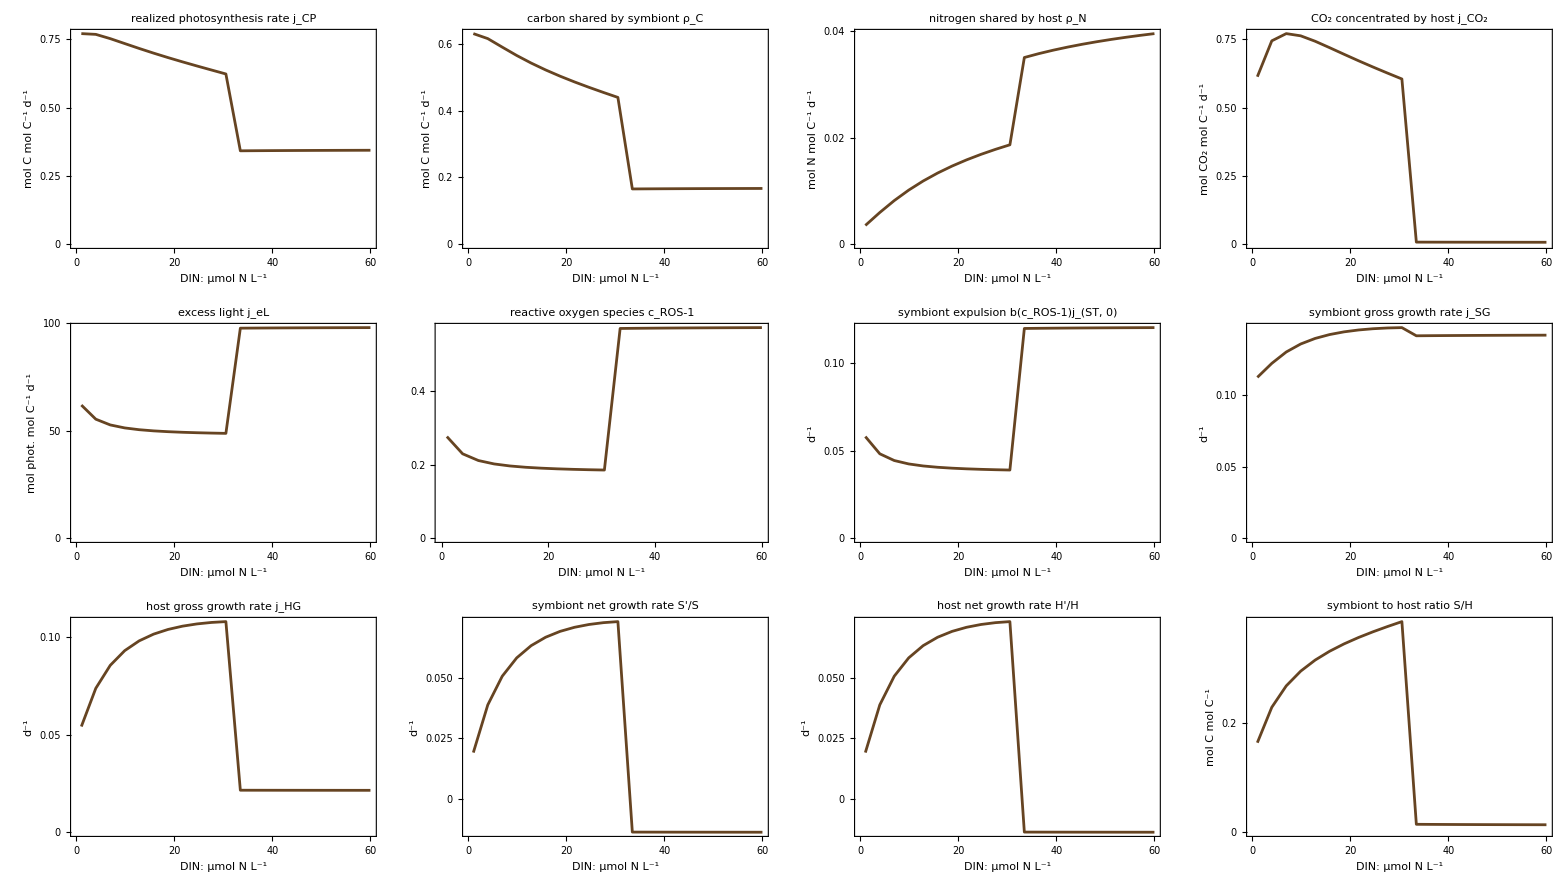
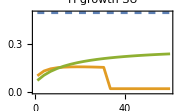
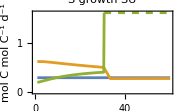
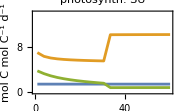

```mathematica
TforNSteadyState=31;
parvalsFvFmArrNSteadyStates=Join[{T->TforNSteadyState},parvalsFvFmArr];
finalΝoptions={_->{AxesOrigin->{0,0},Ticks->{ticksmanual,ticksmanual},ImagePadding->{{55,25},{40,5}}}};
finalplot["steadystate-FvFm-Arr-N-high-jHGm.pdf",parvalsFvFmArrNSteadyStates,Ν,rangeΝFinalStatePlot,inivalsdefault,yranges,arrangementFinalStatePlotN,finalΝoptions,10^6]
finalplot["steadystate-FvFm-Arr-N-low-jHGm.pdf",parvalsFvFmArrNSteadyStates/.{(jHGm->_)->(jHGm->.25)},Ν,rangeΝFinalStatePlot,inivalsdefault,yranges,arrangementFinalStatePlotN,finalΝoptions,10^7]
```

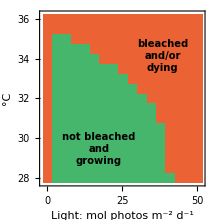
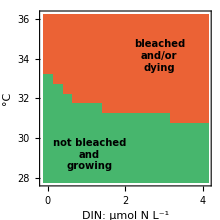
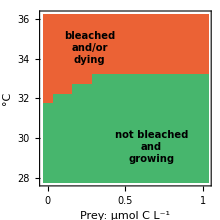
-Graphics- | -Graphics- | -Graphics- |

```mathematica
(*Fig. 6*)
steps=16;
minTemp=28;
maxTemp=36;
meanTemp=Mean[{minTemp,maxTemp}];
rangeTemp=Range[minTemp,maxTemp,(maxTemp-minTemp)/steps];
maxL=5 10;
rangeL=Range[0,maxL,maxL/steps];
maxN=   4 10^-6 ;
maxX=1 10^-6;
meanX=X/.parvalsFvFmArr;
rangeN=Range[0,maxN,  maxN/steps];
rangeX=Range[0,maxX,  maxX/steps];
ConditionsAndColors2Light={#[[1]],Lighter@#[[2]],#[[3]]}&/@ConditionsAndColors2;
epilogstyle={10,Bold};
names2DLong=FinalStatePlotLabel;
multiplier2D={L->1,Ν->10^6,X->10^6};
label1=Column[{"not bleached","and","growing"},Alignment->Center];
label2=Column[{"bleached","and/or","dying"},Alignment->Center];
epilogReplace2D={
L->{{label1,{15 #,8.5 #}},{label2,{32#,32#}}},
Ν->{{label1,{12#,7#}},{label2,{30#,32#}}},
X->{{label1,{28#,9#}},{label2,{12#,34#}}}
}&@(steps/40);
rangeReplace2D={
L->rangeL,
Ν->rangeN,
X->rangeX
};
tmaxFinalContourPlot=1500;
FinalState2DRow[ConditionsAndColors_,parvals_,epilogReplace_,names_]:=
Table[FinalState2DDiscretePlot[parvals,inivalsdefault,ConditionsAndColors,T,parameter,rangeTemp,parameter/.rangeReplace2D,Automatic,{#[[1]],If[Round[#]-#==0,Round[#],#]&@#[[2]]}&/@makeTicks[rangeTemp,4],{#[[1]],If[Round[#]-#==0,Round[#],#]&@((parameter/.multiplier2D)#[[2]])}&/@makeTicks[ (parameter/.rangeReplace2D),4],False,Table[Inset[Style[epi[[1]],epilogstyle],epi[[2]]],{epi,parameter/.epilogReplace}],names2DLong],{parameter,{L,Ν,X}}];
(Export[NotebookDirectory[]<>"/export/2Dplot-maintext.pdf",#];#)&@Row@FinalState2DRow[ConditionsAndColors2,parvalsFvFmArr,epilogReplace2D,names2DLong]
```

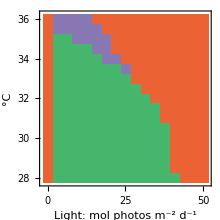
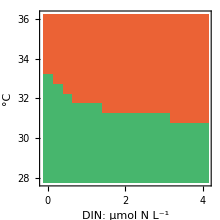
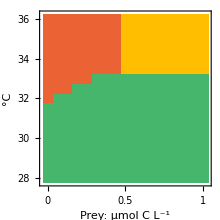
-Graphics- | -Graphics- | -Graphics- |

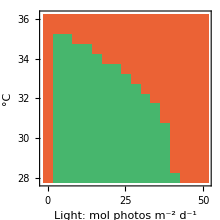
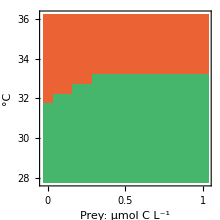
-Graphics- | -Graphics- | -Graphics- |

```mathematica
(*Fig. S13, S14*)
FinalState2DDiscretePlot[ConditionsAndColors_,parvals_]:=
Quiet@Join[{
legendFinalState2DDiscretePlot[ConditionsAndColors]},FinalState2DRow[ConditionsAndColors,parvals,{_->{}},names2DLong]];
FinalState2DDiscretePlotExport[filename_,ConditionsAndColors_,parvals_]:=
(Export[NotebookDirectory[]<>"/export/"<>filename,#];#)&@Column[{#[[1]],Row[#[[2;;-1]]]}&@FinalState2DDiscretePlot[ConditionsAndColors,parvals],Alignment->Center];
FinalState2DDiscretePlotExport["2Dplot4-FvFm-Arr.pdf",ConditionsAndColors,Join[{tmax->tmaxFinalContourPlot},parvalsFvFmArr]]
FinalState2DDiscretePlotExport["2Dplot2-FvFm-Arr.pdf",ConditionsAndColors2,Join[{tmax->tmaxFinalContourPlot},parvalsFvFmArr]]
```

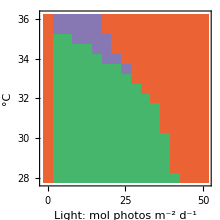
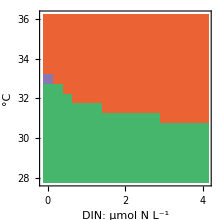
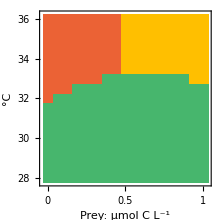
-Graphics- | -Graphics- | -Graphics- |

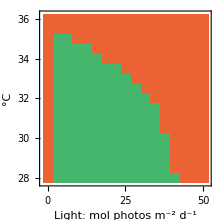
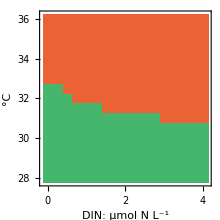
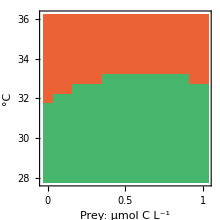
-Graphics- | -Graphics- | -Graphics- |

```mathematica
FinalState2DDiscretePlotExport["2Dplot4-FvFm.pdf",ConditionsAndColors,Join[{tmax->tmaxFinalContourPlot},parvalsFvFm]]
FinalState2DDiscretePlotExport["2Dplot2-FvFm.pdf",ConditionsAndColors2,Join[{tmax->tmaxFinalContourPlot},parvalsFvFm]]
```

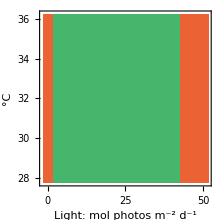
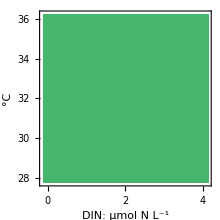
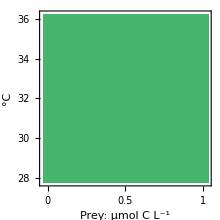
-Graphics- | -Graphics- | -Graphics- |

-Graphics- | -Graphics- | -Graphics- |

```mathematica
FinalState2DDiscretePlotExport["2Dplot4-Arr.pdf",ConditionsAndColors,parvalsArr]
FinalState2DDiscretePlotExport["2Dplot2-Arr.pdf",ConditionsAndColors2,parvalsArr]
```

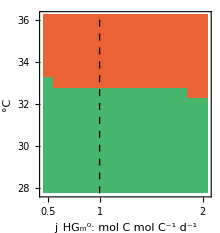
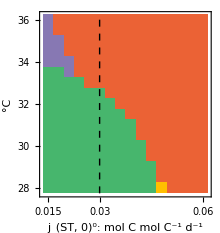
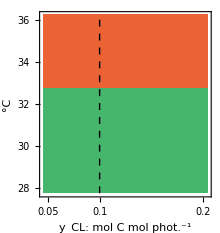
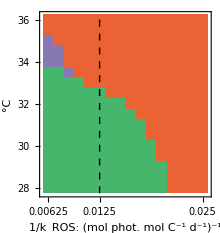
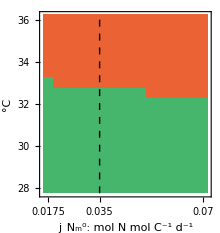
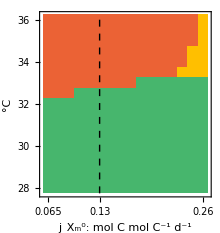
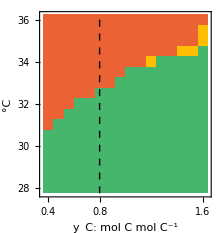
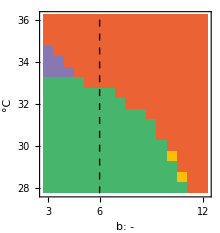
-Graphics- |  | -Graphics- |  | -Graphics- |  | -Graphics- | 
-Graphics- |  | -Graphics- |  | -Graphics- |  | -Graphics- | 
-Graphics- |  | -Graphics- |  | -Graphics- |  | 
-Graphics- |  | -Graphics- |  | -Graphics- |  |

```mathematica
(*Fig. S15*)
rangeparameter[parameter_]:=Range[0.5#,2#,((2-.5)#)/(steps-1)]&@(parameter/.parvalsFvFmArr);
makeTicks2[range_,tickpositions_]:=Table[{i,N[range⟦i⟧]},{i,tickpositions}];
sensitivityPlot[parameter_]:=FinalState2DDiscretePlot[parvalsFvFmArr,inivalsdefault,ConditionsAndColors,T,parameter,rangeTemp,rangeparameter[parameter],Automatic,{#[[1]],If[Round[#]-#==0,Round[#],#]&@#[[2]]}&/@makeTicks[rangeTemp,4],{#[[1]],If[Round[#]-#==0,Round[#],#]&@#[[2]]}&/@makeTicks2[ rangeparameter[parameter],{1,6,16}],False,{Dashed,Thick,Line[{{(steps-1)/(2(2-.5))+.5,0},{(steps-1)/(2(2-.5))+.5,steps+1}}]},(#[[1]]->Row[{#[[2]],": ",#[[1]]/.units}]&/@Join[namesShort,units])];
(Export[NotebookDirectory[]<>"/export/sensitivity-analysis.pdf",#];#)&@Column[{
legendFinalState2DDiscretePlot[ConditionsAndColors],
Multicolumn[Table[
sensitivityPlot[parameter],
{parameter,{jHGm0,jNm0,jSGm0,j0HT0,j0ST0,jXm0,jCPm0,kCO2,yCL,yC,astar,kNPQ,OneOverkROS,b}}
],4]
},Alignment->Center]
```